## Code for generating Figures

## Figure 1

This function was pre-defined to eliminate error messages when correlating vectors that are all zero.

```mathematica
SpecialCorrelation[v1_, v2_]:= If[Length[Union[v1]]==1 ∨ Length[Union[v2]]==1, 0, Correlation[v1,v2]]
```

### Figure 1 A-B

Datasets plotted were generated using the following code, where λ was substituted with a value between 0.01 and 10, as shown in the figure legend

```mathematica
Table[SpecialCorrelation@@Table[N [RandomVariate[PoissonDistribution[λ],500]],2],{50000}]
```

### Figure 1 C

Additional atasets plotted were generated using the following code, where λ was substituted with a value of 0.1, 0.05 or 0.025, and c was set to 0.5.

```mathematica
Table[SpecialCorrelation@@Table[N [RandomVariate[PoissonDistribution[RandomVariate[LogNormalDistribution[Log[λ/(√(1+c^2))],√Log[1+c^2]]]],500]],2],{50000}];
```

### Figure 1 D

the following code was used to generate a distribution of sequencing depths for 500 cells, as shown in the inset to panel D

```mathematica
depths=Table[RandomVariate[LogNormalDistribution[Log[0.5/(√(1+1.5^2))],√Log[1+1.5^2]]],500]
```

### Figure 1 E

The following code was used to generate the data for the histograms.  The first formula generates data for the normalized data.  The second formula generates data for the equal sequencing depth case.

```mathematica
Table[Correlation@@Table[(N [RandomVariate[PoissonDistribution[#]]]&/@depths)/depths,2],{10000}];
Table[Correlation@@Table[N [RandomVariate[PoissonDistribution[1],500]],2],{10000}]
```

## Figure 2

Here we create toy data to see how scRNAseq data should be distributed under the null hypothesis, factoring in differential sequencing depth and stochasticity of gene expression.  

For each simulation, we will consider 1000 genes and 999 cells.  Each gene g_i has a target gene expression level of  t_i, that varies from 0.1 molecule per cell to 10000 molecules per cell, i.e. 5 orders of magnitude.  For simplicity we will distribute the target gene expression values evenly (in a logarithmic sense) across those values

```mathematica
targets=Table[10^i, {i, -1.455,3.54, 0.005}];
```

Next we generate a list of sequencing depths for each cell that mimics typicaly ranges of sequencing depth in scRNAseq

```mathematica
depths=0.05*With[{σ=0.75, δ=0.00100},Table[Exp@(-√2 σ InverseErfc[2 y]), {y,δ,1-δ,δ}]];
```

```mathematica
Length[depths]
```

999

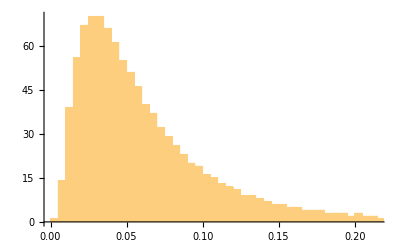

```mathematica
Histogram[depths, {0.005}]
```

Simulated data was then created using this code

```mathematica
simulatedData=Map[N[RandomVariate[PoissonDistribution[RandomVariate[LogNormalDistribution[Log[#/(√(1+0.5^2))],√Log[1+0.5^2]]]]]]&,KroneckerProduct[targets, depths],{2}];
```

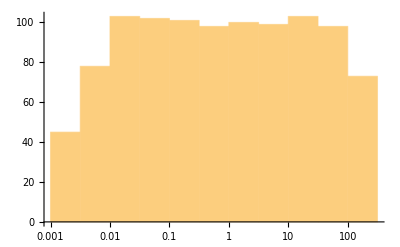

```mathematica
Histogram[Mean/@simulatedData, "Log", PlotRange-> All]
```

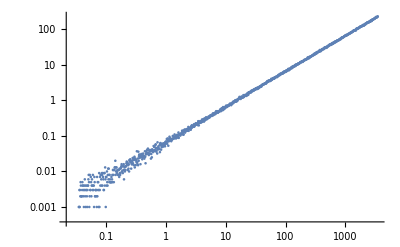

```mathematica
ListLogLogPlot[MapThread[List, {targets,Mean/@simulatedData}]]
```

Then we Sort the data in order of mean values for each gene, and call the output simulatedData1b.  The data were stored in file simulatedData1b.mx

### Panels A - B

```mathematica
simulatedData1b= SortBy[Select[simulatedData, Total[#]>0&], Mean]; Length[simulatedData1b]
```

the file containing these data has been saved under the name simulatedData1b.mx; it is plotted as the blue data points in panel A and B.

Next we generated normalized simulated data by this code:

```mathematica
simulatedData1c=SortBy[#/((Mean/@Transpose[simulatedData1b])/Mean[Flatten[simulatedData1b]])&/@simulatedData1b, Mean];
```

the file containing these data has been saved under the name simulatedData1c.mx; it is plotted as the orange data points in panel A .

BigSur was used to extract values of ϕ’ from simulatedData1b, using different values of the adjustable parameter c.  With c= 0.5, the data are plotted as red points in panel A and green points in panel B.  With c=0.2, the data are plotted as orange points in panel B and with c= 0.8 as red points in panel B.  

Finally, simulatedData1b were subjected to normalization via SCTransform (Hafemeister and Satija, 2019), using default parameters.  Data were transformed by applying -1+ E^x, to restore integer values.  

The output was saved under the name simulatedData1bSCT.mtx.

### Panel C

BigSur (with c=0.5) was used to obtain the matrix of gene-gene PCC’ values, and their p-values, for the non-normalized data, simulatedData1b.mx

The following code was used to generate matrices of PCC from normalized data, i.e.  simulateddata1c.mx; p-values were determined emprically.

```mathematica
SparseArray[LowerTriangularize[ Correlation[Transpose[simulatedData1c]],-1]];
```

## Figure 3

Droplet based sequencing data from Torre et al. 2018, were downloaded, and formated into matpac format.  (Geo accession GSE99330). 
Genes in which fewer than 8 cells contained any UMI were removed.  
Pseudogenes were then removed.  Lists of pseudogenes were compiled from HGNC and BioMart.  
The resulting matpac contained 14,933 genes and 8640 cells and can be found in the file rajDropSeq4.mx.

Values of PCC' and associated p - values were returned by BigSur (using c=0.5, which was determined to be the best fit choice for c).  
Values of uncorrected PCCs were obtained as in Figure 2.

## Figure 4

### Panel A

The results of running BigSur (with c=0.5) on the matpac from rajDropSeq4.mx were used to identify statistically significant gene-gene correlations, and create a list of 878 gene communities, 96 of which contained 4 or more genes.  The lengths of these were, in decreasing order:

{2160,1570,392,235,213,87,85,70,56,34,19,15,14,13,11,10,9,9,9,9,8,7,7,7,6,6,6,6,6,6,6,6,6,6,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}

The full list of communities was saved in file significantCommunities.mx

It was observed, by inspection, that the first two communities show strong anticorrelation with each other.  This was plotted using the visualization function NewPlotSingle, without cutoff (i.e. all significant correlations shown), with formatting by spring electrical embedding.  Vertices representing genes from community 1 (which includes nearly all mitochondrially encoded genes) were colored in light blue; those from community 2 (which includes nearly all ribosomal genes) were colored in light brown.

### Panel B

The 8640 cells from rajDropSeq4.mx were subclustered into three clusters using the results from BigSur referred to above.  The function MostStronglyConnected was used to pick out the 50 most strongly connected genes in communities 1 and 2.  These were

{AKAP9,ANKRD11,ATM,ATP1A1,BOD1L1,CCDC14,CHD4,COX6A1,CSPG4,DDX17,DST,GABPB1-AS1,GOLGB1,HP1BP3,IGF2R,LAMB1,LUC7L3,MACF1,MT-ATP6,MT-ATP8,MT-CO1,MT-CO2,MT-CO3,MT-CYB,MT-ND1,MT-ND2,MT-ND3,MT-ND4,MT-ND4L,MT-ND5,MT-ND6,MT-RNR1,MT-RNR2,MT-TF,MT-TL1,MT-TP,MT-TT,MT-TV,MYH10,NEAT1,PAXBP1,PMEL,PNISR,PRKDC,PSAP,RRBP1,SON,SPEN,SRRM2,SRSF11}

from community 1 and

{CD63,FTH1,FTL,GAPDH,PRDX1,RPL11,RPL12,RPL13,RPL13A,RPL19,RPL23,RPL24,RPL26,RPL27,RPL27A,RPL28,RPL30,RPL31,RPL34,RPL35,RPL35A,RPL37,RPL37A,RPL38,RPL8,RPLP0,RPLP1,RPLP2,RPS11,RPS12,RPS13,RPS14,RPS15,RPS16,RPS18,RPS19,RPS2,RPS20,RPS21,RPS23,RPS24,RPS27A,RPS29,RPS3,RPS5,RPS6,RPS8,SNHG5,TPT1,UBA52}

from community 2.  Theses lists were then merged.

The rows of the cell-specific residuals matrix returned by BigSur that corresponded to these 100 genes were then extracted, and the data were subjected to PC-based clustering using SNNGraph.  The results were subjected to Leiden clustering (resolution 0.25) to generate the UMAP shown.  The cell IDs corresponding to the three identified communities can be found in the file cluster IDs 1_2_3.mx.

### Panels C-E

Cluster 1 from panel B was subjected to further subclustering by the same procedure.  The matpac was first subsetted to include only cells from cluster 1 (c-value was determined to be 0.25).  802 gene communities were identified, of which 74 had greater than 3 genes.  CollapseCommunitiesRecursive was used to aggregate small into large communities so that the total number of communities was reduced to 602, of which 128 were of length greater than 3 genes.  The first and third of these communities contained most of the mitochondrially-encoded and ribosomal subunit genes, respectively.  The function MostStronglyConnected was used to pick out the 50 most strongly connected genes in communities 1 and 3.  These were

{AKAP9,ARGLU1,ATP1A1,CYTL1,DDX5,DST,EIF4A2,EIF4G1,EPRS,FUS,HPS4,LAMB1,LGALS3BP,LRPAP1,MACF1,MT-ATP6,MT-ATP8,MT-CO1,MT-CO2,MT-CO3,MT-CYB,MT-ND1,MT-ND2,MT-ND3,MT-ND4,MT-ND4L,MT-ND5,MT-ND6,MT-RNR1,MT-TF,MT-TL1,MT-TP,MT-TS2,MYH10,PDIA6,PEG10,PLCB4,PMEL,PNISR,PRKDC,PSAP,RRBP1,SF3B1,SPEN,SPTBN1,SRRM2,TLN1,TYR,UBR5,ZMYND8}

and

{ALDOA,ATP5E,ATP5EP2,EIF3E,GAPDH,GAS5,LRRC75A,LRRC75A-AS1,NACA,NACA2,PABPC1,PABPC3,RP11-452N17.1,RPL11,RPL12,RPL23,RPL26,RPL27,RPL27A,RPL28,RPL30,RPL31,RPL35,RPL37,RPL37A,RPL38,RPL8,RPLP1,RPLP2,RPS11,RPS12,RPS13,RPS14,RPS16,RPS17,RPS18,RPS19,RPS20,RPS21,RPS23,RPS24,RPS27A,RPS3,RPS6,RPS8,RPSA,RPSAP58,UQCRH,UQCRHL,ZFAS1}

Theses lists were then merged .  The rows of the cell-specific residuals matrix returned by BigSur that corresponded to these 100 genes were then extracted, and the data were subjected to PC-based clustering using SNNGraph.  The results were subjected to Leiden clustering (resolution 0.15) to generate the UMAP shown.  The cell IDs corresponding to the two identified communities can be found in the file cluster IDs 1.1_1.2.mx.

```mathematica
Export["cluster IDs 1.1_1.2.mx",Thread[{"cluster 1.1", "cluster 1.2"}-> Import["cellsubsets01NewVer6.mx"]]]
```

cluster IDs 1.1_1.2.mx

For panels C-D the following genes the following lists of genes were first taken to be all the mitochondrially-encoded and all the ribosomal subunits in the genome, respectively

{MT-ATP6,MT-ATP8,MT-CO1,MT-CO2,MT-CO3,MT-CYB,MT-ND1,MT-ND2,MT-ND3,MT-ND4,MT-ND4L,MT-ND5,MT-ND6,MT-RNR1,MT-RNR2,MT-TA,MT-TC,MT-TD,MT-TE,MT-TF,MT-TG,MT-TH,MT-TI,MT-TL1,MT-TL2,MT-TM,MT-TP,MT-TQ,MT-TR,MT-TS1,MT-TS2,MT-TT,MT-TV,MT-TW,MT-TY}

{RPL10,RPL10A,RPL10L,RPL11,RPL12,RPL13,RPL13A,RPL14,RPL15,RPL17,RPL18,RPL18A,RPL19,RPL21,RPL22,RPL22L1,RPL23,RPL23A,RPL24,RPL26,RPL26L1,RPL27,RPL27A,RPL28,RPL29,RPL3,RPL30,RPL31,RPL32,RPL34,RPL34-AS1,RPL35,RPL35A,RPL35AP25,RPL36,RPL36A,RPL36AL,RPL37,RPL37A,RPL38,RPL39,RPL39L,RPL3L,RPL4,RPL5,RPL6,RPL7,RPL7A,RPL7L1,RPL8,RPL9,RPLP0,RPLP1,RPLP2,RPS10,RPS11,RPS12,RPS13,RPS14,RPS15,RPS15A,RPS16,RPS17,RPS18,RPS19,RPS19BP1,RPS20,RPS21,RPS23,RPS24,RPS25,RPS26,RPS27,RPS27A,RPS27L,RPS28,RPS29,RPS3A,RPS4X,RPSAP58}

For each cell in each cluster, we totaled the number of mitochondrial, or ribosomal UMI in that cell, and plotted it as shown in panels C and D, respectively, agains the total UMI in that cell.  

Panel E displays summary statistics for the further analysis of all cell subsets by BigSur.

## Figure 5

NewPlotDouble was used to visualize the positive and negative interactions among the mitochondrially - encoded and ribosomal subunit genes (or glycolysis genes) in each of the clusters indicated.  The ribosomal and mitochondrial gene lists used were as in Fig. 4C-D.

## Figure 6

the following gene lists were used in this figure:

Reactome Cholesterol (from MSigDB “curated” collection):  ACAT2,ARV1,CYP51A1,DHCR24,DHCR7,EBP,FDFT1,FDPS,GGPS1,HMGCR,HMGCS1,HSD17B7,IDI1,IDI2,LBR,LSS,MSMO1,MVD,MVK,NSDHL,PPAPDC2,PMVK,SC5D,SQLE,SREBF1,SREBF2,TM7SF2

Extended Cholesterol (from MSigDC “hallmark” collection, except for ACLY):
ABCA2,ACAT2,ACLY,ACSS2,ACTG1,ADH4,ALCAM,ALDOC,ANTXR2,ANXA13,ANXA5,ATF3,ATF5,ATXN2,AVPR1A,CBS,CD9,CHKA,CLU,CPEB2,CTNNB1,CXCL16,CYP51A1,DHCR7,EBP,ECH1,ERRFI1,ETHE1,FABP5,FADS2,FASN,FBXO6,FDFT1,FDPS,GLDC,GNAI1,GPX8,GSTM2,GUSB,HMGCR,HMGCS1,HSD17B7,IDI1,JAG1,LDLR,LGALS3,LGMN,LPL,LSS,MAL2,MVD,MVK,NFIL3,FAM129A,NSDHL,PCYT2,PDK3,PLAUR,PLSCR1,PMVK,PNRC1,PPARG,S100A11,SC5D,SCD,SEMA3B,SQLE,SREBF2,STARD4,STX5,TM7SF2,TMEM97,TNFRSF12A,TP53INP1,TRIB3

to the above list we added in ACLY, a key enzyme in generating Acetyl-CoA for cholesterol biosynthesis, which was identified as a central part of a cholesterol module by Blattman et al., (10.1016/j.cels.2017.11.002 )

### Panels A - B

A : Significantly positively correlated gene - pairs that involved any member of the reactome cholesterol list were identified from the output of significantly correlated pairs produced by the analysis of cluster 1.2 by BigSur .  
B : The matpac for cluster 1.2 was subjected to  normalization by sequencing depth, and (uncorrected) Pearson Correlation Coefficients were calculated for all gene - gene pairs .  To obtain a dataset of correlations that included the same number of reactome cholesterol genes as in panel A, only positive correlations with PCC > 0.29 were kept .  All positive correlations involving a reactome cholesterol gene and any genes of this set are shown .

### Panel C-E

The following code was used to count up "in" and "out" links

```mathematica
Options[InOut]={"Positive Only"-> True};
InOut[gNO_, genes_,  cutoff_, OptionsPattern[]]:=
Module[{mat,posns,posns2,in,out},
mat=If[OptionValue["Positive Only"],SparseArray[BoolEval[gNO[[3]]> cutoff], {Length[gNO[[3]]], Length[gNO[[3]]]}],SparseArray[BoolEval[Abs[gNO[[3]]]> cutoff], {Length[gNO[[3]]], Length[gNO[[3]]]}]];
posns= Flatten[Position[gNO[[2]],#]&/@genes];
in=mat[[posns, posns]]["ExplicitLength"];
posns2 = Complement[Range[Length[mat]],posns];
out = SparseArray[RestoreSymmetryExceptDiagonal[mat]][[posns, posns2]]["ExplicitLength"];
{in,out} ]
```

InOut takes as input a gno (which contains a matrix of significant correlations), a list of genes, and a correlation coefficient threshold.  It returns the number of above-threshold significant correlations within members of that list of genes, and the number of above-threshold significant correlations between members of that list of genes and other genes.

In panel C, this function was applied to the gnos used in panels A (BigSur) and B (uncorrected PCCs), using the reactome cholesterol gene set.

In panel D, a similar analysis was carried out using additional gene sets :

glycolysis→{ABCB6,ADORA2B,AGL,AGRN,AK3,AK4,AKR1A1,ALDH7A1,ALDH9A1,ALDOA,ALDOB,ALG1,ANG,ANGPTL4,ANKZF1,ARPP19,ARTN,AURKA,B3GALT6,B3GAT1,B3GAT3,B3GNT3,B4GALT1,B4GALT2,B4GALT4,B4GALT7,BIK,BPNT1,CACNA1H,CAPN5,CASP6,CD44,CDK1,CENPA,CHPF,CHPF2,CHST1,CHST12,CHST2,CHST4,CHST6,CITED2,CLDN3,CLDN9,CLN6,COG2,COL5A1,COPB2,CTH,CXCR4,CYB5A,DCN,DDIT4,DEPDC1,DLD,DPYSL4,DSC2,ECD,EFNA3,EGFR,EGLN3,ELF3,ENO1-IT1,ENO2,ERO1L,EXT1,EXT2,FAM162A,FBP2,FKBP4,FUT8,G6PD,GAL3ST1,GALE,GALK1,GALK2,GAPDHS,GCLC,GFPT1,TSTA3,GLCE,GLRX,GMPPA,GMPPB,GNE,GNPDA1,GOT1,GOT2,GPC1,GPC3,GPC4,GPR87,GUSB,GYS1,GYS2,HAX1,HDLBP,HK2,HMMR,HOMER1,HS2ST1,HS6ST2,HSPA5,IDH1,IDUA,IER3,IGFBP3,IL13RA1,IRS2,ISG20,KDELR3,KIF20A,KIF2A,LCT,LDHA,LDHC,LHPP,LHX9,MDH1,MDH2,ME1,ME2,MED24,MERTK,MET,MIF,MIOX,MPI,MXI1,NANP,NASP,NDST3,NDUFV3,NOL3,NSDHL,NT5E,P4HA1,P4HA2,PAM,PAXIP1,PC,PDK3,PFKFB1,PFKP,PGAM1,PGAM2,PGK1,PGLS,PGM2,PHKA2,PKM,PKP2,PLOD1,PLOD2,PMM2,POLR3K,PPFIA4,PPIA,PPP2CB,PRPS1,PSMC4,PYGB,PYGL,QSOX1,RARS,RBCK1,RPE,RRAGD,SAP30,SDC1,SDC2,SDC3,SDHC,SLC16A3,SLC25A10,SLC25A13,SLC35A3,SLC37A4,SOD1,SOX9,SPAG4,SRD5A3,STC1,STC2,STMN1,TALDO1,TFF3,TGFA,TGFBI,TKTL1,TPBG,TPI1,TPST1,TXN,UGP2,VCAN,VEGFA,VLDLR,XYLT2,ZNF292}

DNA repair→{AAAS,ADA,ADCY6,ADRM1,AGO4,AK1,AK3,ALYREF,APRT,ARL6IP1,BCAM,BCAP31,BOLA2,BRF2,CANT1,CCNO,CDA,CETN2,CLP1,CMPK2,COX17,CSTF3,DAD1,DCTN4,DDB1,DDB2,DGCR8,DGUOK,DUT,EDF1,EIF1B,ELL,TCEB3,ERCC1,ERCC2,ERCC3,ERCC4,ERCC5,ERCC8,FEN1,GMPR2,GPX4,DFNA5,GTF2A2,GTF2B,GTF2F1,GTF2H1,GTF2H3,GTF2H5,GTF3C5,GUK1,HCLS1,HPRT1,IMPDH2,ITPA,LIG1,MPC2,MPG,MRPL40,NCBP2,NELFB,NELFCD,NELFE,NFX1,NME1,NME3,NME4,NPR2,NT5C,NT5C3A,NUDT21,NUDT9,PCNA,PDE4B,PDE6G,PNP,POLA1,POLA2,POLB,POLD1,POLD3,POLD4,POLE4,POLH,POLL,POLR1C,POLR1D,ZNRD1,POLR2A,POLR2C,POLR2D,POLR2E,POLR2F,POLR2G,POLR2H,POLR2I,POLR2J,POLR2K,POLR3C,POLR3GL,POM121,PRIM1,RAD51,RAD52,RAE1,RALA,RBX1,REV3L,RFC2,RFC3,RFC4,RFC5,RNMT,RPA2,RPA3,RRM2B,SAC3D1,SDCBP,SEC61A1,SF3A3,SMAD5,SNAPC4,SNAPC5,SRSF6,SSRP1,STX3,SUPT4H1,SUPT5H,SURF1,TAF10,TAF12,TAF13,TAF1C,TAF6,TAF9,TARBP2,TK2,TMED2,TP53,TSG101,TYMS,UMPS,UPF3B,USP11,VPS28,VPS37B,VPS37D,XPC,ZNF707,ZWINT}

p53 targets→{ABAT,ABCC5,ABHD4,ACVR1B,ADA,AEN,AK1,ALOX15B,ANKRA2,APAF1,APP,ATF3,BAIAP2,BAK1,BAX,BLCAP,BMP2,BTG1,BTG2,CASP1,CCND2,CCND3,CCNG1,CCNK,CCP110,CD81,CD82,CDH13,CDK5R1,CDKN1A,CDKN2A,CDKN2AIP,CDKN2B,CEBPA,CGRRF1,CLCA2,ADCK3,CSRNP2,CTSD,CTSF,CYFIP2,DCXR,DDB2,DDIT3,DDIT4,DEF6,DGKA,DNTTIP2,DRAM1,EI24,IKBKAP,EPHA2,EPHX1,EPS8L2,ERCC5,F2R,FAM162A,FAS,FBXW7,FDXR,FGF13,FOS,FOXO3,FUCA1,GADD45A,GLS2,GM2A,GPX2,HIST1H1C,H2AFJ,H2AW,HBEGF,HDAC3,HEXIM1,HINT1,HMOX1,HRAS,HSPA4L,IER3,IER5,IFI30,IL1A,INHBB,IP6K2,IRAG2,IRAK1,ISCU,ITGB4,JAG2,JUN,KIF13B,KLF4,KLK8,KRT17,LDHB,LIF,MAPKAPK3,MDM2,MKNK2,MXD1,MXD4,NDRG1,NHLH2,NINJ1,NOL8,NOTCH1,NUDT15,NUPR1,OSGIN1,PCNA,PDGFA,PERP,PHLDA3,PIDD1,PITPNC1,PLK2,PLK3,PLXNB2,PMM1,POLH,POM121,PPM1D,PPP1R15A,PRKAB1,PRMT2,PROCR,PTPN14,PTPRE,PVT1,RAB40C,GNB2L1,RAD51C,RAD9A,RALGDS,RAP2B,RB1,RCHY1,RETSAT,RGS16,RHBDF2,RNF19B,RPL18,RPL36,RPS12,RPS27L,RRAD,RRP8,RXRA,S100A10,S100A4,SAT1,SDC1,SEC61A1,SERPINB5,SERTAD3,SESN1,SFN,SLC19A2,SLC35D1,SLC3A2,SLC7A11,SOCS1,SP1,SPHK1,ST14,STEAP3,STOM,TAP1,TAX1BP3,TCHH,TCN2,TGFA,TGFB1,TM4SF1,TM7SF3,TNFSF9,TNNI1,TOB1,TP53,TP63,TPD52L1,TPRKB,TRAF4,TRAFD1,TRIAP1,TRIB3,TSC22D1,TSPYL2,TXNIP,UPP1,VAMP8,VDR,VWA5A,WRAP73,WWP1,XPC,ZBTB16,ZFP36L1,ZMAT3,ZNF365}

Unfolded Protein Response→{ALDH18A1,ARFGAP1,ASNS,ATF3,ATF4,ATF6,ATP6V0D1,BAG3,BANF1,CALR,CCL2,CEBPB,CEBPG,CHAC1,CKS1B,CNOT2,CNOT4,CNOT6,CXXC1,DCP1A,DCP2,DCTN1,DDIT4,DDX10,DKC1,DNAJA4,DNAJB9,DNAJC3,EDC4,EDEM1,EEF2,EIF2AK3,EIF2S1,EIF4A1,EIF4A2,EIF4A3,EIF4E,EIF4EBP1,EIF4G1,ERN1,ERO1L,EXOC2,EXOSC1,EXOSC10,EXOSC2,EXOSC4,EXOSC5,EXOSC9,FKBP14,FUS,GEMIN4,GOSR2,H2AFX,HERPUD1,HSP90B1,HSPA5,HSPA9,HYOU1,IARS,IFIT1,IGFBP1,IMP3,KDELR3,KHSRP,KIF5B,LSM1,LSM4,MTHFD2,SKIV2L2,NABP1,NFYA,NFYB,NHP2,NOLC1,NOP14,NOP56,NPM1,PAIP1,PARN,PDIA5,PDIA6,POP4,PREB,PSAT1,RPS14,RRP9,SDAD1,SEC11A,SEC31A,SERP1,SHC1,SLC1A4,SLC30A5,SLC7A5,SPCS1,SPCS3,SRPR,SRPRB,SSR1,STC2,TARS,TATDN2,TSPYL2,TTC37,TUBB2A,VEGFA,WFS1,WIPI1,XBP1,XPOT,YIF1A,YWHAZ,ZBTB17}

Hypoxia→{ACKR3,ADM,ADORA2B,AK4,AKAP12,ALDOA,ALDOB,ALDOC,AMPD3,ANGPTL4,ANKZF1,ANXA2,ATF3,ATP7A,B3GALT6,B4GALNT2,BCAN,BCL2,BGN,STRA13,BNIP3L,BRS3,BTG1,CA12,CASP6,CAV1,PTRF,PRKCDBP,CCN1,CTGF,WISP2,CCNG2,CDKN1A,CDKN1B,CDKN1C,CHST2,CHST3,CITED2,COL5A1,CP,CSRP2,CXCR4,DCN,DDIT3,DDIT4,DPYSL4,DTNA,DUSP1,EDN2,EFNA1,EFNA3,EGFR,ENO1-IT1,ENO2,ENO3,ERO1L,ERRFI1,ETS1,EXT1,F3,FAM162A,FBP1,FOS,FOSL2,FOXO3,GAA,GALK1,GAPDH,GAPDHS,GBE1,GCK,GCNT2,GLRX,GPC1,GPC3,GPC4,GPI,GRHPR,GYS1,HAS1,HDLBP,HEXA,HK1,HK2,HMOX1,HOXB9,HS3ST1,HSPA5,IDS,IER3,IGFBP1,IGFBP3,IL6,ILVBL,INHA,IRS2,ISG20,JMJD6,JUN,KDELR3,KDM3A,KIF5A,KLF6,KLF7,KLHL24,LALBA,LARGE,LDHA,LDHC,LOX,LXN,MAFF,MAP3K1,MIF,MT1E,MT2A,MXI1,MYH9,NAGK,NCAN,NDRG1,NDST1,NDST2,NEDD4L,NFIL3,CCRN4L,NR3C1,P4HA1,P4HA2,PAM,PCK1,PDGFB,PDK1,PDK3,PFKFB3,PFKL,PFKP,PGAM2,PGF,PGK1,PGM1,PGM2,PHKG1,PIM1,PKLR,PKP1,PLAC8,PLAUR,PLIN2,PNRC1,PPARGC1A,PPFIA4,PPP1R15A,PPP1R3C,PRDX5,PRKCA,PYGM,RBPJ,RORA,RRAGD,S100A4,SAP30,SCARB1,SDC2,SDC3,SDC4,SELENBP1,SERPINE1,SIAH2,SLC25A1,SLC2A1,SLC2A3,SLC2A5,SLC37A4,SLC6A6,SRPX,STBD1,STC1,STC2,SULT2B1,TES,TGFB3,TGFBI,TGM2,TIPARP,TKTL1,TMEM45A,TNFAIP3,TPBG,TPD52,TPI1,TPST2,UGP2,VEGFA,VHL,VLDLR,WSB1,XPNPEP1,ZFP36,ZNF292}

Reactive Oxygen Species→{ABCC1,ATOX1,CAT,CDKN2D,EGLN2,ERCC2,FES,FTL,G6PD,GCLC,GCLM,GLRX,GLRX2,GPX3,GPX4,GSR,HHEX,HMOX2,IPCEF1,JUNB,LAMTOR5,LSP1,MBP,MGST1,MPO,MSRA,NDUFA6,NDUFB4,NDUFS2,NQO1,OXSR1,PDLIM1,PFKP,PRDX1,PRDX2,PRDX4,PRDX6,PRNP,PPP2R4,SBNO2,SCAF4,VIMP,SOD1,SOD2,SRXN1,STK25,TXN,TXNRD1,TXNRD2}

PI3K Akt mTOR Signaling→{ACACA,ACTR2,ACTR3,ADCY2,AKT1,AKT1S1,AP2M1,ARF1,ARHGDIA,ARPC3,ATF1,CAB39,CAB39L,CALR,CAMK4,CDK1,CDK2,CDK4,CDKN1A,CDKN1B,CFL1,CLTC,CSNK2B,CXCR4,DAPP1,DDIT3,DUSP3,E2F1,ECSIT,EGFR,EIF4E,FASLG,FGF17,FGF22,FGF6,GNA14,GNGT1,GRB2,ADRBK1,GSK3B,HRAS,HSP90B1,IL2RG,IL4,IRAK4,ITPR2,LCK,MAP2K3,MAP2K6,MAP3K7,MAPK1,MAPK10,MAPK8,MAPK9,MAPKAP1,MKNK1,MKNK2,MYD88,NCK1,NFKBIB,NGF,NOD1,PAK4,PDK1,PFN1,PIK3R3,PIKFYVE,PIN1,PITX2,PLA2G12A,PLCB1,PLCG1,PPP1CA,PPP2R1B,PRKAA2,PRKAG1,PRKAR2A,PRKCB,PTEN,PTPN11,RAC1,RAF1,RALB,RIPK1,RIT1,RPS6KA1,RPS6KA3,RPTOR,SFN,SLA,SLC2A1,SMAD2,SQSTM1,STAT2,TBK1,THEM4,TIAM1,TNFRSF1A,TRAF2,TRIB3,TSC2,UBE2D3,UBE2N,VAV3,YWHAB}

Mitotic spindle→{ABI1,ABL1,ABR,ACTN4,AKAP13,ALMS1,ALS2,ANLN,APC,ARAP3,ARF6,ARFGEF1,ARFIP2,ARHGAP10,ARHGAP27,ARHGAP29,ARHGAP4,ARHGAP5,ARHGDIA,ARHGEF11,ARHGEF12,ARHGEF2,ARHGEF3,ARHGEF7,ARL8A,ATG4B,AURKA,BCAR1,BCL2L11,BCR,BIN1,BIRC5,BRCA2,BUB1,CAPZB,CCDC88A,CCNB2,CD2AP,CDC27,CDC42,CDC42BPA,CDC42EP1,CDC42EP2,CDC42EP4,CDK1,CDK5RAP2,CENPE,CENPF,CENPJ,CEP131,CEP192,CEP250,CEP57,CEP72,CKAP5,CLASP1,CLIP1,CLIP2,CNTRL,CNTROB,CSNK1D,CTTN,CYTH2,DLG1,DLGAP5,DOCK2,DOCK4,DST,DYNC1H1,DYNLL2,ECT2,EPB41,EPB41L2,ESPL1,EZR,FARP1,FBXO5,FGD4,FGD6,FLNA,FLNB,FSCN1,GEMIN4,GSN,HDAC6,HOOK3,INCENP,ITSN1,KATNA1,KATNB1,KIF11,KIF15,KIF1B,KIF20B,KIF22,KIF23,KIF2C,KIF3B,KIF3C,KIF4A,KIF5B,KIFAP3,KLC1,KNTC1,KPTN,LATS1,LLGL1,LMNB1,LRPPRC,MAP1S,MAP3K11,MAPRE1,MARCKS,MARK4,MID1,MID1IP1,MYH10,MYH9,MYO1E,MYO9B,NCK1,NCK2,NDC80,NEDD9,NEK2,NET1,NF1,NIN,NOTCH2,NUMA1,NUSAP1,OPHN1,PAFAH1B1,PALLD,PCGF5,PCM1,PCNT,PDLIM5,PIF1,PKD2,PLEKHG2,PLK1,PPP4R2,PRC1,PREX1,PXN,RAB3GAP1,RABGAP1,RACGAP1,RALBP1,RANBP9,RAPGEF5,RAPGEF6,RASA1,RASA2,RASAL2,RFC1,RHOF,RHOT2,RICTOR,ROCK1,SAC3D1,SASS6,9-Sep,SHROOM1,SHROOM2,SMC1A,SMC3,SMC4,SORBS2,SOS1,SPTAN1,SPTBN1,SSH2,STAU1,STK38L,SUN2,SYNPO,TAOK2,TBCD,TIAM1,TLK1,TOP2A,TPX2,TRIO,TSC1,TTK,TUBA4A,TUBD1,TUBGCP2,TUBGCP3,TUBGCP5,TUBGCP6,UXT,VCL,WASF1,WASF2,WASL,YWHAE}

In panel E, we generated results similar to those in panel D, except using 10 “random” gene sets.  To generate random gene sets, we picked lists of genes of length 150 from among only those genes with average raw expression across all cells in cluster 1.2 that was greater than 0.052.  As the number of cells in cluster 1.2 is 1582, this means >82 UMI total across all cells.  This was done to ensure that the median gene expression in the random gene sets was similar to the median expression for genes in the union of all of the gene sets used in panel D.

## Supplementary Figures

### S1 and S2

Full results for data for analyses shown in Figures 3 C and 3 D, respectively

### S3

Histogram of equivalent PCC values obtained by application of BigSur as in Fig. 3

### S4 - S7

NewPlotSingle was used to visualize significant correlations within communities identified by BigSur within cluster 1.2.  In some cases smaller communities were aggregated into larger one.  Graphs labeled “PPI” use orange highlighting to show correlations that correspond to known protein-protein interactions.  The list of gene-pairs used for identifying protein protein interactions is described in the next section.

## PPI and Paralog Overlap

To calculate the overlap between significanly correlated gene pairs and gene pairs previously known to either interact physically, or represent paralogous genes, we generated lists of known interacting genes and paralog pairs as follows:

### Protein-proteins interactions

A file of 790,008 interacting pairs ppiPairsAll.csv was compiled from two databases, STRING and HIPPIE (http://cbdm-01.zdv.uni-mainz.de/~mschaefer/hippie/ ).

The STRING database was queried using BIOMART, and only experimentally validated protein-protein interactions were retrieved.  

Of these, we used only those 523,292 pairs involving genes both of which were present in the matpac being analyzed (for trivial reasons, a gene pair  involving  a gene not in the matpac could never be found among correlated gene pairs derived from that matpac)

### Paralog Pairs

Human paralog pairs were those identified in Hu et al, 2022.  https://doi.org/10.1016/j.csbj.2022.11.041.  The list of 3,132 pairs can be found in the the file paralogs.csv.
Of these, 1,425 contained only genes that were both present in the matpacs analyzed.